### Example of use of “StateDiagrams.m”

#### Initialization

Loads the StateDiagrams.m package (change the directory to the folder you are using)

```mathematica
Directory[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"StateDiagrams_mma-v12.m"
```

A list of the available functions in the package is obtained by the command:

```mathematica
Names["Dependability`StateDiagrams`*"]
```

{ArrangeMatrix,DownTimeDensity,DownTimeDensityLaplace,GenHomogeneousSystem,KoutofN,KoutofNMode,KroenSum,LabelList,MDT,MergeStates,MTBF,MTFF,MTTF,MUT,ParallelMode,PlotDiagram,ProbStationary,ProbTransient,RelFunc,SeriesMode,SetDiagonal,StepPlot,UnAvailability}

Check syntax in the examples in task 1 below, and by ?UnAvailability, etc.. of mouseover.
-Graphics-

```mathematica
?SeriesMode
?KoutofNMode
```

## Lab 4: Dependability modelling

## Students: August Heltne-Karlson and Erik Turøy Midtun

### System description

In  this  part  you  are  going  to  develop  an  analytic  model  with  the  objective  to  study  the  dependability  with respect to airport availability and time until reopening of a runway after a snowfall.

In the modelling of the airport in this assignment you need reliability block diagrams and Markov models [see Chapter 7 in the textbook].

### Task 1: Model of two plowing trucks [warm-up, 0%]

The  main purpose of this task is to apply the Mathematica add-on package “StateDiagrams.m” to obtain transient steady state probabilities, and metrics such as (un)availability, reliability, MTBF, etc.

The example is the part of the airport that consists of two plow trucks.  
The trucks might break down (intensity λ_1) and need to be repaired (intensity μ_1).  
If both trucks have failed, no plowing can be conducted and this sub-system is down (with huge consequences when it starts snowing of  cause).

Following the description of “Matrix form” in “Section 5.2.4 Steady state solution” (also presented in the lecture and in the lecture notes from Nov 3) of the textbook, we will get a set of equations on a matrix form. 
1.1. Define the system state variable(s) and corresponding events and make a Markov model of the trucks as described above.
1.2. Define the transition intensity matrix of the trucks
1.3. Define operation modus of the three states  (this means, available/unavailable,  up/down, working/failed)
1.4. Plot the diagram as defined - compare against the figure from 1.1 to check if you have implemented the model correctly (states, transitions, and intensities)
1.5. Determine the transient and steady state probabilities 
1.6. Obtain symbolical expressions for transient (U(t),R(t)) and steady state measures (U,MTFF,MTTF,MTBF)
1.7. Provide numerical values of the measures
1.8. Plot the transient and steady state unavailability as a function of t - what do you observe?

```mathematica
(*
1.1. Define the system state variable(s) and corresponding events and make a Markov model of the trucks as described above.
state = number of failed trucks, events are truck failures and repair 
*)
```

-Graphics-

```mathematica
(*
1.2. Define the transition intensity matrix of the trucks
*)
(* initialise an empty 3x3 matrix *) 
𝒬=Table[",",{3},{3}]; 
(* assign intensities to all transitions, null to non-transitions *) 
𝒬[[1,2]]=2 Subscript[λ, 1]; (* assign failure rate *)
𝒬[[1,3]]=0; (* non-transition *)
𝒬[[2,1]]=Subscript[μ, 1];(* assign repair rate *)
𝒬[[2,3]]=Subscript[λ, 1]; (* assign failure rate *)
𝒬[[3,1]]=0;(* non-transition *)
𝒬[[3,2]]=2 Subscript[μ, 1]; (* assign repair rate *)
Subscript[ℳ, 1]= SetDiagonal[Transpose[𝒬]];(* add the diagonal elements, see Sect 5.2.4 *)
Subscript[ℳ, 1]//MatrixForm  (* Print nicely on matrix form *)
```

(-2 λ_1 | μ_1 | 0
2 λ_1 | -λ_1-μ_1 | 2 μ_1
0 | λ_1 | -2 μ_1)

```mathematica
(*
1.3. Define operation modus of the three states (True=up/working, False=down/failed)
*)
Subscript[ℒ, 1]={"Ok 
[1]", "1 down
[2]", "Both down
[3]"}; (* labelling states - alternative to just 1,2,3 *)
Subscript[𝒲, 1]={True, True, False};
```

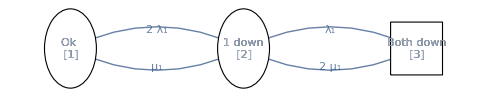

```mathematica
(*
1.4. Plot the diagram as defined - compare with figure above
*)
PlotDiagram[Subscript[ℳ, 1],Subscript[𝒲, 1],Subscript[ℒ, 1]]
```

```mathematica
(*
1.5. Determine the transient and steady state probabilities 
*)
(* transient probabilities, defined a function of t *)
P[t_]:=ProbTransient[Subscript[ℳ, 1],{1,0,0},x] /. {x-> t}
(* show the funtion *)
P[t]
(* steady state probabilities *)
Subscript[PS, 1]=ProbStationary[Subscript[ℳ, 1]]
```

{(ⅇ^(-2 t (λ_1+μ_1)) (λ_1+ⅇ^(t (λ_1+μ_1)) μ_1)^2)/(λ_1+μ_1)^2,(2 ⅇ^(-2 t (λ_1+μ_1)) (-1+ⅇ^(t (λ_1+μ_1))) λ_1 (λ_1+ⅇ^(t (λ_1+μ_1)) μ_1))/(λ_1+μ_1)^2,((-1+ⅇ^(-t (λ_1+μ_1)))^2 λ_1^2)/(λ_1+μ_1)^2}

{μ_1^2/(λ_1+μ_1)^2,(2 λ_1 μ_1)/(λ_1+μ_1)^2,λ_1^2/(λ_1+μ_1)^2}

```mathematica
(*
1.6. Obtain symbolical expressions for transient (U(t),R(t)) and steady state measures (U,MTFF,MTTF,MTBF)
*)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,1] (* reliability function *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] (* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] (* Mean Time Between Failures *)
(* Unavailability, U(t), U *)
U[t_]:=UnAvailability[P[t],Subscript[𝒲, 1]] (* transient U(t) *)
U[t]
(*** Check assymptotic behaviour of U(t) when t->infinity ***)
Limit[U[t],{t-> Infinity}, Assumptions->Subscript[λ, 1]+Subscript[μ, 1]>0]
UnAvailability[Subscript[PS, 1],Subscript[𝒲, 1]] (* steady state *)
```

(ⅇ^(-1/2 t (3 λ_1+μ_1+√(λ_1^2+6 λ_1 μ_1+μ_1^2))) ((1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) λ_1^2+μ_1 ((1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) μ_1+(-1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) √(λ_1^2+6 λ_1 μ_1+μ_1^2))+3 λ_1 (2 (1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) μ_1+(-1+ⅇ^(t √(λ_1^2+6 λ_1 μ_1+μ_1^2))) √(λ_1^2+6 λ_1 μ_1+μ_1^2))))/(2 (λ_1^2+6 λ_1 μ_1+μ_1^2))

1/λ_1-(-λ_1-μ_1)/(2 λ_1^2)

((λ_1+μ_1) (4 λ_1+μ_1))/(2 λ_1^2 (2 λ_1+μ_1))

(λ_1+μ_1)^2/(2 λ_1^2 μ_1)

((-1+ⅇ^(-t (λ_1+μ_1)))^2 λ_1^2)/(λ_1+μ_1)^2

λ_1^2/(λ_1+μ_1)^2

λ_1^2/(λ_1+μ_1)^2

```mathematica
(*
1.7. Numerical values of the measures
Use these parameter sets 
*)
Subscript[𝒫, 11]= {Subscript[λ, 1]-> 0.1, Subscript[μ, 1]->1}
Subscript[𝒫, 12]= {Subscript[λ, 1]-> 0.5, Subscript[μ, 1]->1}

ProbStationary[Subscript[ℳ, 1]]/. Subscript[𝒫, 11] (* solve symbolically first -> then make numerical *)
ProbStationary[(Subscript[ℳ, 1] /. Subscript[𝒫, 11])] (* RECOMMENDED FOR LARGE MODELS: make matrix numerical first -> then solve *)

(* Subscript[𝒫, 11]= {Subscript[λ, 1]-> 0.1, Subscript[μ, 1]->1} *)
UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 11] (* transient *)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,0] /. Subscript[𝒫, 11] (* reliability function *)
UnAvailability[PS,Subscript[𝒲, 1]] /. Subscript[𝒫, 11](* steady state *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] /. Subscript[𝒫, 11](* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 11] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 11] (* Mean Time Between Failures *)

(* Subscript[𝒫, 12]= {Subscript[λ, 1]-> 0.5, Subscript[μ, 1]->1} *)
UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12] (* transient *)
RelFunc[Subscript[ℳ, 1],Subscript[𝒲, 1],t,1] /. Subscript[𝒫, 12] (* reliability function *)
UnAvailability[PS,Subscript[𝒲, 1]] /. Subscript[𝒫, 12](* steady state *)
MTFF[Subscript[ℳ, 1],Subscript[𝒲, 1],1] /. Subscript[𝒫, 12](* Mean Time to First Failure *)
MTTF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 12] (* Mean Time To Failure *)
MTBF[Subscript[ℳ, 1],Subscript[𝒲, 1]] /. Subscript[𝒫, 12] (* Mean Time Between Failures *)
```

{λ_1→0.1,μ_1→1}

{λ_1→0.5,μ_1→1}

{0.826446,0.165289,0.00826446}

{0.826446,0.165289,0.00826446}

0.00826446 (-1+ⅇ^(-1.1 t))^2

0.310559 ⅇ^(-1.28443 t) (1+ⅇ^(1.26886 t)+1.26886 (-1+ⅇ^(1.26886 t))+0.01 (1+ⅇ^(1.26886 t))+0.3 (1.26886 (-1+ⅇ^(1.26886 t))+2 (1+ⅇ^(1.26886 t))))

PS.{0,0,1}

65.

64.1667

60.5

0.111111 (-1+ⅇ^(-1.5 t))^2

0.117647 ⅇ^(-2.28078 t) (1+ⅇ^(2.06155 t)+2.06155 (-1+ⅇ^(2.06155 t))+0.25 (1+ⅇ^(2.06155 t))+1.5 (2.06155 (-1+ⅇ^(2.06155 t))+2 (1+ⅇ^(2.06155 t))))

PS.{0,0,1}

5.

4.5

4.5

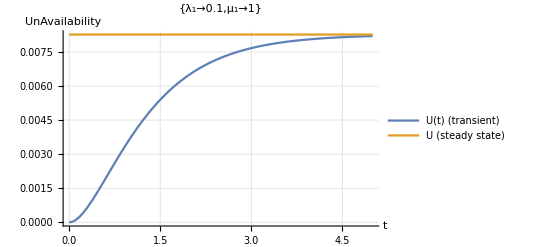

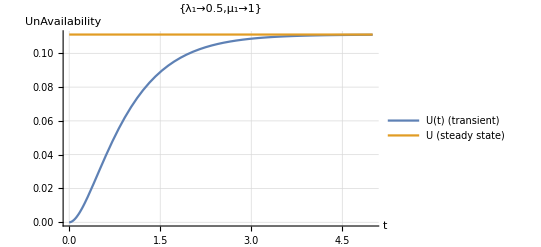

```mathematica
(* 
1.8. Plot the transient steady state unavailability as a function of t - what do you observe? 
*)
Plot[{
Legended[UnAvailability[P[t]/. Subscript[𝒫, 11],Subscript[𝒲, 1]],"U(t) (transient)"], 
Legended[UnAvailability[Subscript[PS, 1]/. Subscript[𝒫, 11],Subscript[𝒲, 1]],"U (steady state)"]},
{t,0,5},PlotRange->All, PlotLabel-> Subscript[𝒫, 11],AxesLabel->{Automatic,UnAvailability}, GridLines->Automatic]
Plot[{
Legended[UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12],"U(t) (transient)"], 
Legended[UnAvailability[Subscript[PS, 1],Subscript[𝒲, 1]]/. Subscript[𝒫, 12],"U (steady state)"]},
{t,0,5},PlotRange->All, PlotLabel-> Subscript[𝒫, 12],AxesLabel->{Automatic,UnAvailability}, GridLines->Automatic]
```

```mathematica
(* When to the unavailabilty exceed the tolerance level of 5%, using the set Subscript[𝒫, 12]? *)
FindRoot[(UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12])-0.05 == 0, {t,0.1}]
NSolve[(UnAvailability[P[t],Subscript[𝒲, 1]]/. Subscript[𝒫, 12])== 0.05 , t,Reals]
```

{t→0.740768}

{{t→-0.34221},{t→0.740768}}

### Task 2: Probability of open runways after snow fall [25%]

You are going to make a model to obtain the transient probability q_i(t) that  i runways are open at time t.  
Assume that 
- you have two runways, and that no trucks fail during plowing,  
- the expected snowing time is  1/κ  and plowing time is 1/γ,
- when both runways are cleaned and reopened, it is assumed that snowing stops
	(this means that we are only interested in the time until first reopening after the snow fall closed the airport), and
- two trucks can not plow the same runways simultaneously.

The objective is to study the transient period from closing both runways at t=0, and until the airport is partly (1 runway), and fully reopened (both runways).

2.1. Define the system state variable(s) and corresponding events and make a Markov model to obtain the transient state probabilities for n trucks.
The system state variables are  the number of available runways. The corresponding events are plowing the runways and snowing filling up the runways.
-Graphics-

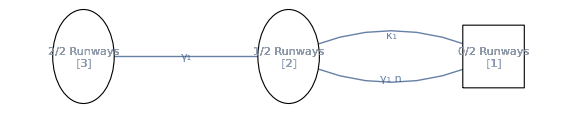

```mathematica
𝒬=Table[",",{3},{3}]; 
𝒬[[1,2]]=n*Subscript[γ, 1]; 
𝒬[[1,3]]=0; 
𝒬[[2,1]]=Subscript[κ, 1]; 
𝒬[[2,3]]=Subscript[γ, 1];
𝒬[[3,1]]=0;
𝒬[[3,2]]=0; 
Subscript[ℳ, 2]= SetDiagonal[Transpose[𝒬]];
Subscript[ℒ, 2]={
"0/2 Runways\n[1]", 
"1/2 Runways\n[2]",
"2/2 Runways\n[3]"}; 
Subscript[𝒲, 2]={False, True, True};  
PlotDiagram[Subscript[ℳ, 2],Subscript[𝒲, 2],Subscript[ℒ, 2]]
```

2.2. Use the package provided to obtain the probability q_i(t) that  i runways are reopened at time t, given that they were closed at t=0 after a heavy snow fall (general for n trucks).

```mathematica
Subscript[P, 2][t_]:=ProbTransient[Subscript[ℳ, 2],{1,0,0},x] /. {x-> t}
Subscript[P, 2][t] //Simplify;
For[i=0,i<3,i++,Print["q",i ,"=",Take[Subscript[P, 2][t],{i+1}]//Simplify, "\n\n"]]
```

q0={1/(2 ((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (-1+n)^2 γ_1^2+κ_1 ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))+γ_1 (2 (1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (1+n) κ_1-(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) (-1+n) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))}

q1={(ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) (-1+ⅇ^(t √(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) n γ_1)/(√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))}

q2={1/(2 (-4 n γ_1^2+((1+n) γ_1+κ_1)^2))ⅇ^(-1/2 t (γ_1+n γ_1+κ_1+√(-4 n γ_1^2+((1+n) γ_1+κ_1)^2))) (-(1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) (-1+n)^2 γ_1^2-κ_1 ((1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-(1+n) γ_1 (2 (1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))-2 ⅇ^(1/2 t ((1+n) γ_1+κ_1+√((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))) κ_1+(-1+ⅇ^(t √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2))) √((-1+n)^2 γ_1^2+2 (1+n) γ_1 κ_1+κ_1^2)))}\n\n

2.3. Plot q_1(t) and q_2(t) for n=1 and n=2 and compare the results.  Use {γ→0.1,κ→1/60}[1/minutes]
	Plot all state probabilities for the first two hours (120 minutes) and discuss what you observe.  Use {γ→ 0.1,κ→ 1/60} [1/minutes]

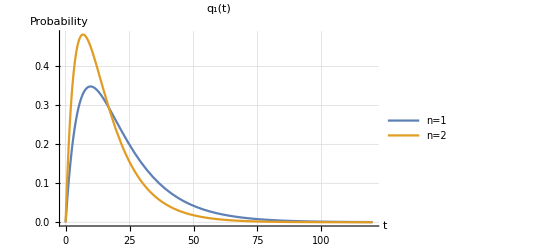

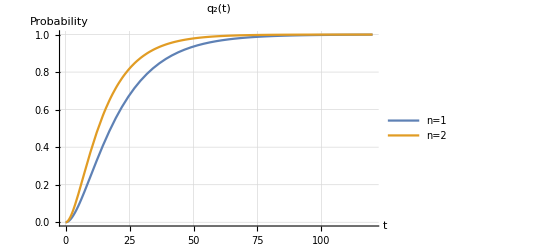

```mathematica
Subscript[𝒫, 11]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->1};
q0n1[t_]=Take[Subscript[P, 2][t],{1}]/. Subscript[𝒫, 11]//Simplify;
q1n1[t_]=Take[Subscript[P, 2][t],{2}]/. Subscript[𝒫, 11]//Simplify;
q2n1[t_]=Take[Subscript[P, 2][t],{3}]/. Subscript[𝒫, 11]//Simplify;

Subscript[𝒫, 12]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->2};
q0n2[t_]=Take[Subscript[P, 2][t],{1}]/. Subscript[𝒫, 12]//Simplify;
q1n2[t_]=Take[Subscript[P, 2][t],{2}]/. Subscript[𝒫, 12]//Simplify;
q2n2[t_]=Take[Subscript[P, 2][t],{3}]/. Subscript[𝒫, 12]//Simplify;

Plot[{
Legended[q1n1[t],"n=1"],
Legended[q1n2[t],"n=2"]},
{t,0,120},PlotRange->All, PlotLabel-> "q_1(t)",AxesLabel->{Automatic, "Probability"}, GridLines->Automatic]

Plot[{
Legended[q2n1[t],"n=1"],
Legended[q2n2[t],"n=2"]},
{t,0,120},PlotRange->All, PlotLabel-> "q_2(t)",AxesLabel->{Automatic,"Probability"}, GridLines->Automatic]
```

With (n=2) two plow trucks we see that in the beginning the probability of being in state 1, the state with no runways available, is lower than in the case with only one truck. We also see that with two trucks we get to the steady state(100% probability for both runways available) faster than with one truck. The overall availability is thus higher with two trucks.

Furthermore, find the maximum reopening time T_max for which the probability is ≥0.95,  P(T<T_max)≥0.95.
	  Compare n=1 and n=2.

```mathematica
Subscript[root, n1]=FindRoot[(q2n1[Subscript[t, 1]])-0.95 == 0, {Subscript[t, 1],0.1}] ;
Subscript[root, n2] = FindRoot[(q2n2[Subscript[t, 2]])-0.95 == 0, {Subscript[t, 2],0.1}];
Print["n=1: ",Subscript[root, n2]]
Print["n=2: ",Subscript[root, n2] ]
Print["Difference t_1 and t_2: ",Subscript[t, 1] -Subscript[t, 2]/. Subscript[root, n1] /. Subscript[root, n2] , "min (", ((Subscript[t, 1] -Subscript[t, 2])/Subscript[t, 1] /. Subscript[root, n1] /. Subscript[root, n2] )*100, "%)"]
```

n=1: {t_2→39.8451}

n=2: {t_2→39.8451}

Difference t_1 and t_2: 13.8314min (25.7681%)

The maximum time needed to fully reopen (2/2 runways) with at least 95% probability is a lot faster when having two trucks instead of one. We can see that two trucks reopens at approximately 14 minutes(~26%) faster than when only having one truck.

2.4. Compare the expected time until first reopening with n=1 and n=2. 
	Plot the relative difference in the expected time until first reopening (gain) for n=1 and n=2 as the expected snowing time 1/κ changes. 
We can use MTFF if we change the model to be {True, True, False} instead of {False, True, True}.

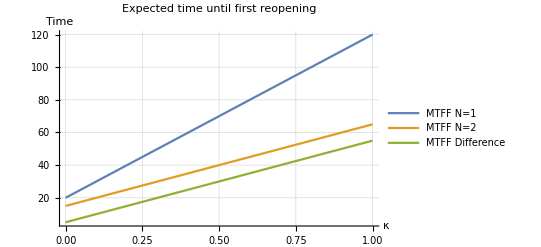

```mathematica
Subscript[𝒫, n1]= {n->1};
Subscript[𝒫, n2]= {n->2};
Subscript[𝒫, 24]= {Subscript[γ, 1]-> 1/10};
Subscript[𝒲, 24]={True,True, False};  
mtffN1=MTFF[Subscript[ℳ, 2],Subscript[𝒲, 24]] /. Subscript[𝒫, n1] /. Subscript[𝒫, 24] ;
mtffN2=MTFF[Subscript[ℳ, 2],Subscript[𝒲, 24]] /. Subscript[𝒫, n2] /. Subscript[𝒫, 24] ;
mtffN21[k_] :=mtffN1  /.{Subscript[κ, 1]-> k}
mtffN22[k_] :=mtffN2  /.{Subscript[κ, 1]-> k}
diff [k_] := mtffN1 -mtffN2 /.{Subscript[κ, 1]-> k}

Plot[{
Legended[mtffN21[κ],"MTFF N=1"],
Legended[mtffN22[κ],"MTFF N=2"],
Legended[diff[κ],"MTFF Difference"]},
{κ,0,1},PlotRange->All, PlotLabel-> "Expected time until first reopening",AxesLabel->{Automatic,"Time"}, GridLines->Automatic]
```

Discuss the gain you get by adding one truck (n=1 -> n=2) when κ changes. Use {γ→0.1} [1/minutes] 
The smallest difference between MTFF for N1 and MTFF for N2 is 33% at k = 0. As the entire airport will stop if the runways are closed, having the ability to reopen as quickly as possible is very important.  At  κ = 1/60 as used earlier in this task, the difference is approximately 5.8 minutes. If κ = 1/60 means that the runways need to be plowed at average once per hour, this ends up costing the airport almost 70 minutes if it stays open from 08-20. This is most likely a too large time loss for the airport to operate properly and as such we suggest having two trucks as long the it is economically viable.

	What is the minimum and maximum gain (and for which κ value)?

```mathematica
Print["MTTF for N=1: ",mtffN1 //Simplify]
Print["MTTF for N=2: ",mtffN2 //Simplify]
Print["Difference: ",mtffN1 - mtffN2 //Simplify]
```

MTTF for N=1: 20 (1+5 κ_1)

MTTF for N=2: 15+50 κ_1

Difference: 5+50 κ_1

As we can see, the gain is linear. This leads to the minimum gain being where κ = 0 -> diff = 5 and the maximum being where κ = 1 -> 55.

### Task 3: Two plowing trucks with two repairmen who might go on sick-leave [30%]

The repair of the trucks depends on a repairman.  
In the model from task 1 we assumed that we have one repairman per truck.  
However, the repairmen might get sick (intensity ν) and are recovered (intensity ϵ).  
Make the necessary changes in the model from task 1 to take into account that the repair of a truck might get delayed due to (a) sick repairman(men). 

3.1. Define the system state variable(s) and corresponding events, and make a Markov model to obtain state probabilities.
The system state variables are the number of trucks and repairmen available. The corresponding events are trucks failing and getting fixed and the repairmen getting sick and getting better.
-Graphics-

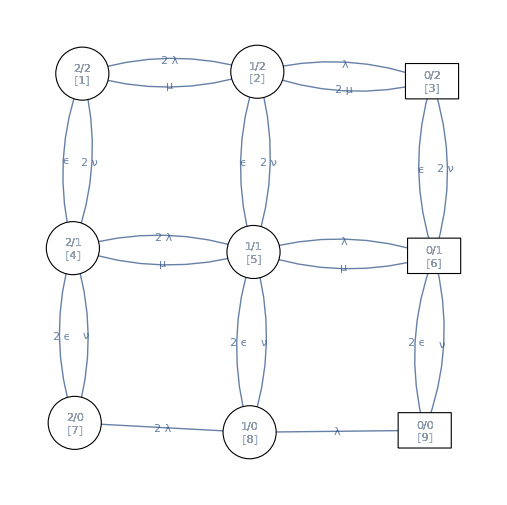

```mathematica
Subscript[Q, 3]= {
{, 2λ,0,2ν,0,    0,      0,0,  0},
{μ,,   λ, 0,     2ν,0,     0,0,  0},
{0,2μ,, 0,     0,     2ν,0,0,  0},
{ϵ,0,  0, ,     2λ,   0,      ν,0,  0},
{0,ϵ,  0, μ,     ,      λ,      0,ν,  0},
{0,0,  ϵ, 0,     μ,      ,      0,0,  ν},
{0,0,  0, 2ϵ, 0,      0,      ,2λ,0},
{0,0,  0, 0,      2ϵ, 0,      0,,   λ},
{0,0, 0,  0,     0,      2ϵ,  0,0,   }
} ;
Subscript[ℳ, 3]=SetDiagonal[Transpose[Subscript[Q, 3]]];
Subscript[ℒ, 3]={"2/2\n[1]","1/2\n[2]","0/2\n[3]",
 "2/1\n[4]", "1/1\n[5]", "0/1\n[6]",
"2/0\n[7]","1/0\n[8]","0/0\n[9]"}; 
Subscript[𝒲, 3]={True, True, False, True, True, False, True, True, False};  
PlotDiagram[Subscript[ℳ, 3],Subscript[𝒲, 3],Subscript[ℒ, 3]]
```

3.2. Use the package provided to obtain the probability that n=0, 1, and 2 trucks are available for 𝒫_2={λ_2→0.1, μ_2 → 1, ν→ 0.01, ϵ →0.5}[1/days]

```mathematica
Subscript[𝒫, 32]={λ->0.1, μ -> 1, ν-> 0.01, ϵ ->0.5};
Subscript[P, 3][t_]:=ProbTransient[(Subscript[ℳ, 3]/. Subscript[𝒫, 32]),{1,0,0,0,0,0,0,0,0},x] /. {x-> t}

Subscript[PS, 31]=ProbStationary[(Subscript[ℳ, 3]/. Subscript[𝒫, 32])] ;
n2 = Take[Subscript[PS, 31],{1}] + Take[Subscript[PS, 31],{4}] + Take[Subscript[PS, 31],{7}];
n2t[t_] = Take[Subscript[P, 3][t],{1}] + Take[Subscript[P, 3][t],{4}] + Take[Subscript[P, 3][t],{7}] //Simplify;
n1 = Take[Subscript[PS, 31],{2}] + Take[Subscript[PS, 31],{5}] + Take[Subscript[PS, 31],{8}];
n1t[t_] = Take[Subscript[P, 3][t],{2}] + Take[Subscript[P, 3][t],{5}] + Take[Subscript[P, 3][t],{8}] //Simplify;
n0= Take[Subscript[PS, 31],{3}] + Take[Subscript[PS, 31],{6}] + Take[Subscript[PS, 31],{9}];
n0t[t_] = Take[Subscript[P, 3][t],{3}] + Take[Subscript[P, 3][t],{6}] + Take[Subscript[P, 3][t],{9}] //Simplify;
Print["n=2\n PS:", n2, "\n P(t):",n2t[t]]
Print["n=1\n PS:", n1, "\n P(t):",n1t[t]]
Print["n=0\n PS:", n0, "\n P(t):",n0t[t]]
```

n=2
 PS:{0.826121}
 P(t):{0.826121+0.00708125 ⅇ^(-2.25089 t)-0.000326728 ⅇ^(-1.97019 t)+0.0120637 ⅇ^(-1.37775 t)-0.0133304 ⅇ^(-1.2145 t)+0.119444 ⅇ^(-1.11537 t)+0.15563 ⅇ^(-1.0313 t)-0.107927 ⅇ^(-1.02 t)+0.00124419 ⅇ^(-0.51 t)}

n=1
 PS:{0.165329}
 P(t):{0.165329-0.0145381 ⅇ^(-2.25089 t)+0.00057375 ⅇ^(-1.97019 t)-0.014617 ⅇ^(-1.37775 t)+0.0148217 ⅇ^(-1.2145 t)-0.110669 ⅇ^(-1.11537 t)-0.127615 ⅇ^(-1.0313 t)+0.0873579 ⅇ^(-1.02 t)-0.000643598 ⅇ^(-0.51 t)}

n=0
 PS:{0.0085491}
 P(t):{0.0085491+0.00745682 ⅇ^(-2.25089 t)-0.000247021 ⅇ^(-1.97019 t)+0.00255327 ⅇ^(-1.37775 t)-0.00149131 ⅇ^(-1.2145 t)-0.00877489 ⅇ^(-1.11537 t)-0.0280144 ⅇ^(-1.0313 t)+0.020569 ⅇ^(-1.02 t)-0.000600595 ⅇ^(-0.51 t)}

3.3. Compare the two models, without (task 1) and with (task 2) repairmen on sick leave with respect to the unavailability and the probability that one truck has failed. 
Change the repair intensity β (assume it partly depends on the skills) and discuss whether it is sufficient to have one truck or if you need two.  
You first need to define what you think is the maximum acceptable probability of not having a truck available.

```mathematica
Subscript[𝒫, 33]={λ->0.1, ν-> 0.01, ϵ ->0.5};
Subscript[PS, 33]=ProbStationary[(Subscript[ℳ, 3]/. Subscript[𝒫, 33])] ;
Subscript[n2, 33][β_] := (Take[Subscript[PS, 33],{1}] + Take[Subscript[PS, 33],{4}] + Take[Subscript[PS, 33],{7}]) /.{μ-> β} ;
Subscript[n1, 33] [β_] :=  (Take[Subscript[PS, 33],{2}] + Take[Subscript[PS, 33],{5}] + Take[Subscript[PS, 33],{8}])/.{μ-> β};
Subscript[n0, 33][β_] :=  (Take[Subscript[PS, 33],{3}] + Take[Subscript[PS, 33],{6}] + Take[Subscript[PS, 33],{9}]) /.{μ-> β};

Subscript[n2, 1] [β_] :=  (Take[Subscript[PS, 1],{1}])/.{Subscript[μ, 1]-> β,Subscript[λ, 1]->0.1}
Subscript[n1, 1] [β_] :=  (Take[Subscript[PS, 1],{2}])/.{Subscript[μ, 1]-> β,Subscript[λ, 1]->0.1}
Subscript[n0, 1][β_] :=  (Take[Subscript[PS, 1],{3}]) /.{Subscript[μ, 1]-> β,Subscript[λ, 1]->0.1}
Grid[{{,,"B=0.5"},{"Task","N0","N1","N2"},{1,Subscript[n0, 1] [0.5],Subscript[n1, 1] [0.5] ,Subscript[n2, 1] [0.5]},{3,Subscript[n0, 33] [0.5],Subscript[n1, 33] [0.5] ,Subscript[n2, 33] [0.5]}}]
Grid[{{,,"B=1"},{"Task","N0","N1","N2"},{1,Subscript[n0, 1] [1],Subscript[n1, 1] [1] ,Subscript[n2, 1] [1]},{3,Subscript[n0, 33] [1],Subscript[n1, 33] [1] ,Subscript[n2, 33] [1]}}]
```

|  | B=0.5 | 
Task | N0 | N1 | N2
1 | {0.0277778} | {0.277778} | {0.694444}
3 | {0.0285189} | {0.277662} | {0.693819}

|  | B=1 | 
Task | N0 | N1 | N2
1 | {0.00826446} | {0.165289} | {0.826446}
3 | {0.00852009} | {0.165334} | {0.826146}

Assuming that the repair intensity 1/day means that it will on average take a day to repair a truck, the airport needs to have two trucks. Having all trucks stop working at the same time means that it will be around a day before you can clear the runway. This would bring a complete halt to all air traffic in the area and is catastrophic for the airport. Therefore having an additional truck to lower the probability that they all fail at the same time and thus decreasing the time between entering the failure state and leaving it is very important for the airport to function over long periods.
TODO maximum acceptable probability

3.4. Obtain the mean time to first failure, and mean time to failure.  Are they the same or different? Why?

```mathematica
MTFF[(Subscript[ℳ, 3]/. Subscript[𝒫, 32]),Subscript[𝒲, 3]]
MTTF[(Subscript[ℳ, 3]/. Subscript[𝒫, 32]),Subscript[𝒲, 3]]
```

64.9673

64.1323

They are different. MTFF is the expected time between node 1(2 trucks and 2 repairmen available) to one of the states with 0 trucks available at t=0. MTTF is the mean time to failure from an arbitrary time when the system is in stationary state and working. As node 2/2 is the most resilient node in the network, MTFF is slightly longer than MTTF as MTTF can start in a less resilient node. The different between them is rather small as node 2/2 is the most probable state to be in

### Task 4: Performability [15%] [no assistance]

The focus in this task is on what is called Performability - “a measurement of how a degradable system performs” [1],[2][3].  
In a performability model you combine the dependability model (here: truck availability model from task 3) with the performance (here: probability of reopening runways from task 2).
Let’s set the guaranteed maximum time to reopen to T_max=45 minutes.  

4.1. What is the probability P(T<T_max) that it takes less than T_max=45 minutes to reopen both runways?  
Calculate it for n=0, 1 and 2 trucks and using  {γ→ 0.1,κ→ 1/60} [1/minutes] from task 2.

```mathematica
Subscript[𝒫, 41]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->0};
q2n0[t_]=Take[Subscript[P, 2][t],{3}]/. Subscript[𝒫, 41]//Simplify;

Subscript[N0T, max]=q2n0[45];
Subscript[N1T, max]=Round[q2n1[45],0.00000001];
Subscript[N2T, max]=Round[q2n2[45],0.0000001];
Print["For N=0: ", Subscript[N0T, max]]
Print["For N=1: ", Subscript[N1T, max]]
Print["For N=2: ", Subscript[N2T, max]]
```

For N=0: {0}

For N=1: {0.91132}

For N=2: {0.96807}

4.2. Combine the probabilities (which are conditioned on n=0,1, and 2) with the model for truck availability from task 3 to obtain the overall probability that it takes less than T_max=45 minutes to reopen both runways.  
Use 𝒫_2={λ_2→0.1, μ_2 → 1, ν→ 0.01, ϵ →0.5} in the truck availability model.

```mathematica
n0t[45]* Subscript[N0T, max] + n1t[45]*Subscript[N1T, max] + n2t[45]*Subscript[N2T, max]
```

{0.950412}

4.3. Which factors contributes to the reopening time?  
Discuss what you would have done if you were asked to reduce the  guaranteed maximum time to reopen to T_max=30 minutes, without changing the guaranteed probability P(T<T_max). 
We cannot do anything with the snowing time κ and we have seen that the effects of repairmen getting sick and better is negligible. So the only factors we can change is the plowing time γ, break down intensity λ and the need to be repaired intensity μ.
Calculate the new probabilities first, identify the factors that contributes, and do a qualitative discussions about (counter)measures that could be taken to ensure that the guaranteed probability P(T<T_max) is provided.

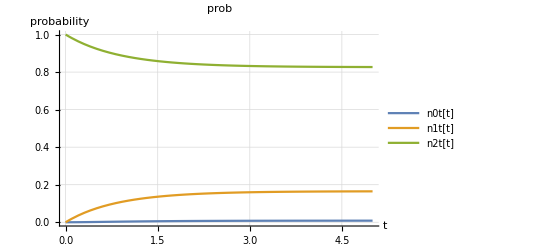

```mathematica
Subscript[𝒫, 43n1]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->1};
Subscript[q2n1, 43][t_]=Take[Subscript[P, 2][t],{3}]/. Subscript[𝒫, 11]//Simplify;

Subscript[𝒫, 43n2]= {Subscript[γ, 1]-> 1/10, Subscript[κ, 1]->1/60, n->2};
Subscript[q2n2, 43][t_]=Take[Subscript[P, 2][t],{3}]/. Subscript[𝒫, 12]//Simplify;

Plot[{
Legended[n0t[t],"n0t[t]"],
Legended[n1t[t],"n1t[t]"],
Legended[n2t[t],"n2t[t]"]},
{t,0,5},PlotRange->All, PlotLabel-> "prob",AxesLabel->{Automatic,"probability"}, GridLines->Automatic]
```

TODO text

### Task 5: Structural model of the whole airport [30%] [no assistance]

The system is “up/working” when 
	- both runways, AND
	- at least 6 of 10 gates, AND
	- one of two deicing stations 
are available.

5.1. What do you have to assume to use a Reliability Block Diagram (RBD)?  What does this mean in the context of the airport system? Is this realistic? 
No rates depend on the system state 
 –Independent failing 
 –Independent repairs / restoration

5.2. Make an Reliability Block Diagram (RBD) of the total airport system
-Graphics-
5.3. Make reliability functions for 
	- R(t,λ) (single component),

```mathematica
R[t_,λ_] = Exp[-λ*t];
```

- R_s(t,n,λ), for an n-serial structure

```mathematica
Subscript[R, s][t_,n_,λ_] = Product[R[t,λ],{i,1,n}];
```

- R_p(t,n,λ), for an n-parallel structure

```mathematica
Subscript[R, p][t_,n_,λ_] = 1-Product[1-R[t,λ],{i,1,n}];
```

- R_kofn(t,k,n,λ), for a k-of-n structure

```mathematica
Subscript[R, kofn][t_,k_,n_, λ_] =∑_(i=k)^n Binomial[n,i]*R[t,λ]^i*(1-R[t,λ])^(n-i);
```

Check function  by 
	Integrate[R_kofn[t,6, 10, λ],{t,0,∞}, Assumptions→λ>0]= 1627/(2520 λ). Which property have you now calculated?

```mathematica
Integrate[Subscript[R, kofn][t,6, 10, λ],{t,0,∞}, Assumptions->λ>0]
```

1627/(2520 λ)

We have calculated the mean time to first failure (MTFF) of the K-of-N system

Explain how R_s(t,n,λ) and R_p(t,n,λ) can be replaced by R_kofn(t,k,n,λ).
R_s is essentially the same as R_kofn with k=n and R_p is R_kofn with k=1. Later when we add more runways than 2, we change the runway reliability function to be R_kofn(t,2,n,λ).

Plot the integral (from 0 to ∞) of Subscript[R, kofn](t,6,10,λ) and Subscript[R, kofn](t,8,10,λ) for  20 values of λ in the range [0,1] (hint:use Table and ListLinePlot)

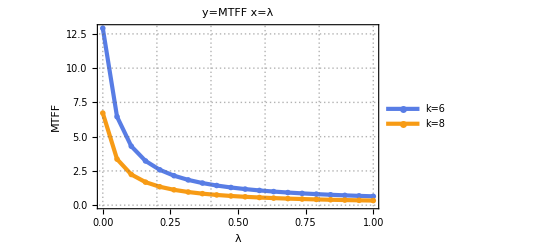

```mathematica
Subscript[k6, 53]=Table[Integrate[Subscript[R, kofn][t,6, 10, λ],{t,0,∞}, Assumptions->λ>0], {λ,1/20,1,1/20}];
Subscript[k8, 53]=Table[Integrate[Subscript[R, kofn][t,8, 10, λ],{t,0,∞}, Assumptions->λ>0], {λ,1/20,1,1/20}];
ListLinePlot[{Subscript[k6, 53],Subscript[k8, 53]},PlotRange->All, PlotLabel-> "y=MTFF x=λ",AxesLabel->{λ,"MTFF"}, GridLines->Automatic, DataRange->{0,1},PlotLegends->{"k=6","k=8"},PlotTheme->"Business"]
```

5.4. Use your reliability functions to determine the R_tot(t) for the airport, compliant with your RBD.

```mathematica
Subscript[R, tot][t_]=(Subscript[R, s][t,2,Subscript[λ, 1]]*Subscript[R, kofn][t,6,10, Subscript[λ, 2]]*Subscript[R, p][t,2,Subscript[λ, 3]])
```

(ⅇ^(-2 t λ_1-6 t λ_2) (1-ⅇ^(-t λ_2))^4 (126-560 ⅇ^(t λ_2)+945 ⅇ^(2 t λ_2)-720 ⅇ^(3 t λ_2)+210 ⅇ^(4 t λ_2)) (1-(1-ⅇ^(-t λ_3))^2))/((-1+ⅇ^(t λ_2))^4)

5.5. Plot R_tot(t) for  𝒫_λ={λ_1→ 0.02,λ_2→ 0.06,λ_3→ 0.1}[1/days]
	What is the probability that the airport runs without interruptions for 1 day, 1 week, and 1 month (including night shifts)?

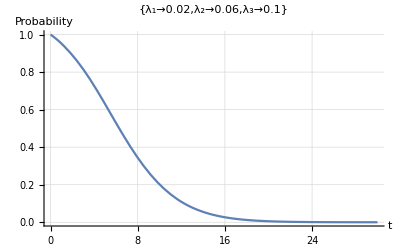

Days | R_tot(%) 𝒫_λ
1 | 95.1963
7 | 43.2636
30 | 0.00682305

```mathematica
Subscript[𝒫, λ]={Subscript[λ, 1]-> 0.02,Subscript[λ, 2]-> 0.06,Subscript[λ, 3]-> 0.1};
Plot[ {Subscript[R, tot][t] /. Subscript[𝒫, λ]},{t,0,30},PlotRange->All, PlotLabel-> Subscript[𝒫, λ],AxesLabel->{Automatic,"Probability"}, GridLines->Automatic]
Grid[{{"Days", "R_tot(%) 𝒫_λ"},{1, (Subscript[R, tot][1] /. Subscript[𝒫, λ])*100},{7, (Subscript[R, tot][7] /. Subscript[𝒫, λ])*100},{30, (Subscript[R, tot][30] /. Subscript[𝒫, λ])*100}},Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}]
```

From the table above, we can see the probabilities that the airport runs without interruption for 1 day, 1week and 1 month.

5.6. What is the main cause of failure?  Which change(s) will have the highest effect?

```mathematica
Grid[{{"Days","Runways", "Gates", "Deicing" },
{1, Subscript[R, s][1,2,0.02],Subscript[R, kofn][1,6,10,0.06], Subscript[R, p][1,2,0.1]},
 {7, Subscript[R, s][7,2,0.02],Subscript[R, kofn][7,6,10,0.06], Subscript[R, p][7,2,0.1]}, 
{30, Subscript[R, s][30,2,0.02],Subscript[R, kofn][30,6,10,0.06], Subscript[R, p][30,2,0.1]
}},Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}]
```

Days | Runways | Gates | Deicing
1 | 0.960789 | 0.999868 | 0.990944
7 | 0.755784 | 0.766748 | 0.746574
30 | 0.301194 | 0.0023331 | 0.0970954

The main cause of failure is dependent on when you examine the system. For T=1, the largest source of failures are the runways as a single runway going down is enough to cause a system failure. For T=7, there’s no main source of failures as all the parts have around the same probability of staying up. For T = 30, gates is the main source of failures as it has a far lower probability of still working compared to runways and deicing stations.

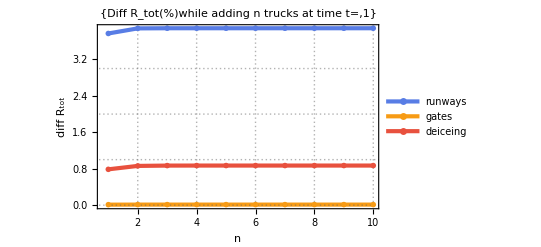
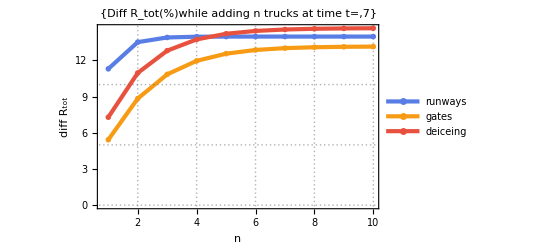
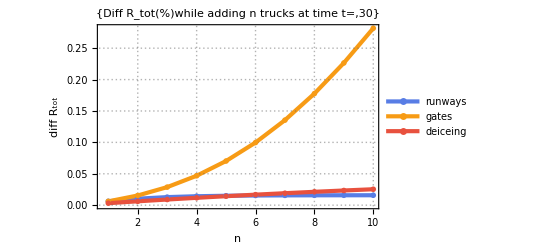

Days | R_tot(%) 𝒫_original | Diff +1R | Diff +1G | Diff +1D
1 | 95.1963 | 3.77003 | 0.0112117 | 0.78718
7 | 95.1963 | -40.6286 | -46.5049 | -44.6399
30 | 0.00682305 | 0.00615697 | 0.00609144 | 0.00315892

```mathematica
Subscript[R, tot2][t_]=100*(Subscript[R, kofn][t,2,Subscript[n, 1],Subscript[λ, 1]]*Subscript[R, kofn][t,6,Subscript[n, 2], Subscript[λ, 2]]*Subscript[R, p][t,Subscript[n, 3],Subscript[λ, 3]]) /. Subscript[𝒫, λ];
Subscript[𝒫, original]={Subscript[n, 1]-> 2,Subscript[n, 2]-> 10,Subscript[n, 3]-> 2};
Subscript[𝒫, RN3]={Subscript[n, 1]-> 3,Subscript[n, 2]-> 10,Subscript[n, 3]-> 2};
Subscript[𝒫, GN11]={Subscript[n, 1]-> 2,Subscript[n, 2]-> 11,Subscript[n, 3]-> 2};
Subscript[𝒫, DN3]={Subscript[n, 1]-> 2,Subscript[n, 2]-> 10,Subscript[n, 3]-> 3};

Subscript[R, 1] =(Subscript[R, tot2][1] /. Subscript[𝒫, original]);
Subscript[R, 7] =(Subscript[R, tot2][7] /. Subscript[𝒫, original]);
Subscript[R, 30] =(Subscript[R, tot2][30] /. Subscript[𝒫, original]);
Subscript[Rrunways, 56][t_]=Table[(Subscript[R, tot2][t] /. {Subscript[n, 1]-> 2+n,Subscript[n, 2]-> 10,Subscript[n, 3]-> 2}) - Subscript[R, t],{n,1,10}];
Subscript[Rgates, 56][t_]=Table[(Subscript[R, tot2][t] /. {Subscript[n, 1]-> 2,Subscript[n, 2]-> 10+n,Subscript[n, 3]-> 2}) - Subscript[R, t],{n,1,10}];
Subscript[Rdeice, 56][t_]=Table[(Subscript[R, tot2][t] /. {Subscript[n, 1]-> 2,Subscript[n, 2]-> 10,Subscript[n, 3]-> 2+n}) - Subscript[R, t],{n,1,10}];

Table[ListLinePlot[{Subscript[Rrunways, 56][t],Subscript[Rgates, 56][t],Subscript[Rdeice, 56][t]},PlotRange->All, PlotLabel->{"Diff R_tot(%)while adding n trucks at time t=", t },AxesLabel->{n,"diff R_tot"}, GridLines->Automatic, DataRange->{1,10},PlotTheme->"Business",PlotLegends->{"runways","gates","deiceing"}],{t,{1,7,30}}]
Grid[{{"Days","R_tot(%) 𝒫_original", "Diff +1R", "Diff +1G", "Diff +1D" },
{1, Subscript[R, 1],(Subscript[R, tot2][1] /. Subscript[𝒫, RN3]) - Subscript[R, 1], (Subscript[R, tot2][1] /. Subscript[𝒫, GN11])-Subscript[R, 1],(Subscript[R, tot2][1] /. Subscript[𝒫, DN3])-Subscript[R, 1]},
 {7, Subscript[R, 1],(Subscript[R, tot2][7] /. Subscript[𝒫, RN3])-Subscript[R, 1], (Subscript[R, tot2][7] /. Subscript[𝒫, GN11]) -Subscript[R, 1], (Subscript[R, tot2][7] /. Subscript[𝒫, DN3])-Subscript[R, 1]},
{30, Subscript[R, 30],(Subscript[R, tot2][30] /. Subscript[𝒫, RN3])-Subscript[R, 30], (Subscript[R, tot2][30] /. Subscript[𝒫, GN11])-Subscript[R, 30], (Subscript[R, tot2][30] /. Subscript[𝒫, DN3])-Subscript[R, 30]
}},Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}]
```

In the plots above we have plotted the difference of R_tot(%) in respect to the different times t=1,7,30 days when changing different values of n.
For t = 1, the largest improvement comes from adding runways. This is because both deicing stations and gates have forms of redundancy and are therefore unlikely to fail day 1. Do note that runways are modelled as 2 out of n.
For t = 7, runways are still the single strongest increase, but deicing stations are catching up for larger n-values.
For t = 30, we can see that the only parameter worth modifying is the number of gates as this yields a relatively large increase for higher values of n. However, while the increase might seem large on the graph, the actual increase is minor at best and resources can most likely be spent better other places than increasing the number of gates.

diff | MTFF+1N | MTFF+2N | MTFF+3N
Runways | 16.6667 | 29.1667 | 39.1667
Gates | 1.51515 | 2.90404 | 4.18609
Deice | 3.33333 | 5.83333 | 7.83333

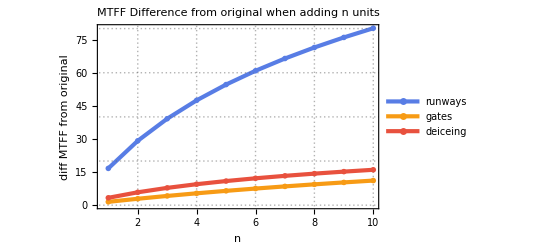

```mathematica
Subscript[MTFF, R]=Integrate[Subscript[R, kofn][t,2, 2, Subscript[λ, 1]] /. Subscript[𝒫, λ],{t,0,∞}];
Subscript[MTFF, G]=Integrate[Subscript[R, kofn][t,6, 10, Subscript[λ, 2]] /. Subscript[𝒫, λ],{t,0,∞}];
Subscript[MTFF, D]=Integrate[Subscript[R, kofn][t,1, 2, Subscript[λ, 3]] /. Subscript[𝒫, λ],{t,0,∞}];

Grid[{{"diff", "MTFF+1N", "MTFF+2N" ,"MTFF+3N" },
{"Runways",  Integrate[Subscript[R, kofn][t,2, 3, Subscript[λ, 1]] /. Subscript[𝒫, λ],{t,0,∞}] - Subscript[MTFF, R],  Integrate[Subscript[R, kofn][t,2, 4, Subscript[λ, 1]] /. Subscript[𝒫, λ],{t,0,∞}] -Subscript[MTFF, R],Integrate[Subscript[R, kofn][t,2, 5, Subscript[λ, 1]] /. Subscript[𝒫, λ],{t,0,∞}] -Subscript[MTFF, R]},
{"Gates",Integrate[Subscript[R, kofn][t,6, 11, Subscript[λ, 2]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, G],  Integrate[Subscript[R, kofn][t,6, 12, Subscript[λ, 2]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, G],Integrate[Subscript[R, kofn][t,6, 13, Subscript[λ, 2]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, G]},
{"Deice",Integrate[Subscript[R, kofn][t,1, 3, Subscript[λ, 3]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, D],  Integrate[Subscript[R, kofn][t,1, 4, Subscript[λ, 3]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, D],Integrate[Subscript[R, kofn][t,1, 5, Subscript[λ, 3]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, D]}
},Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}]

Subscript[MTFFrunways, 56]= Table[Integrate[Subscript[R, kofn][t,2, 2+n, Subscript[λ, 1]] /. Subscript[𝒫, λ],{t,0,∞}] - Subscript[MTFF, R],{n,1,10}];
Subscript[MTFFgates, 56]= Table[Integrate[Subscript[R, kofn][t,6, 10+n, Subscript[λ, 2]] /. Subscript[𝒫, λ],{t,0,∞}]-Subscript[MTFF, G],{n,1,10}];
Subscript[MTFFdeice, 56]= Table[Integrate[Subscript[R, kofn][t,1, 2+n, Subscript[λ, 3]] /. Subscript[𝒫, λ],{t,0,∞}] - Subscript[MTFF, D],{n,1,10}];

ListLinePlot[{Subscript[MTFFrunways, 56],Subscript[MTFFgates, 56],Subscript[MTFFdeice, 56]},PlotRange->All, PlotLabel-> "MTFF Difference from original when adding n units",AxesLabel->{n,"diff MTFF from original"}, GridLines->Automatic, DataRange->{1,10},PlotLegends->{"runways","gates","deiceing"},PlotTheme->"Business"]
```

The reason for the large increases in runway’s MTFF is that it is modelled as 2-out-of-n. Adding more runways results in more redundancy and allows the repairmen much more leeway compared to the original 2-out-of-2. It is worth noting that increasing the amount of runways are both expensive and requires a lot of free space and is therefore not as attractive as it can seem on paper.

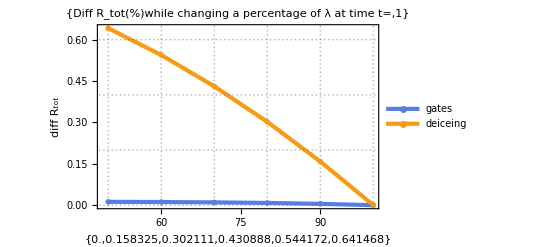
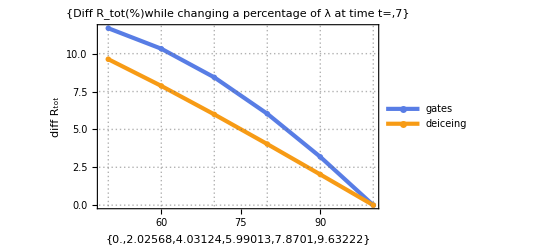
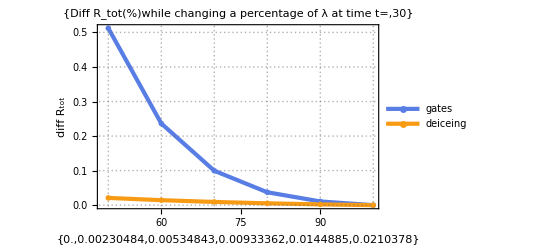

```mathematica
Subscript[R, tot3][t_]=100*(Subscript[R, kofn][t,2,2,Subscript[λ, 1]]*Subscript[R, kofn][t,6,10, Subscript[λ, 2]]*Subscript[R, p][t,2,Subscript[λ, 3]]);

Subscript[𝒫, λ]={Subscript[λ, 1]-> 0.02,Subscript[λ, 2]-> 0.06,Subscript[λ, 3]-> 0.1};
Subscript[λR, 7] =(Subscript[R, tot3][7] /. Subscript[𝒫, λ]);
Subscript[λR, 30] =(Subscript[R, tot3][30] /. Subscript[𝒫, λ]);

Subscript[Rgates, 56λ][t_]=Table[(Subscript[R, tot3][t] /. {Subscript[λ, 1]-> 0.02,Subscript[λ, 2]-> (0.06*i)/100,Subscript[λ, 3]-> 0.1}) - Subscript[λR, t],{i,100,50,-10}];
Subscript[Rdeice, 56λ][t_]=Table[(Subscript[R, tot3][t] /. {Subscript[λ, 1]-> 0.02,Subscript[λ, 2]-> 0.06,Subscript[λ, 3]-> (0.1*i)/100}) - Subscript[λR, t],{i,100,50,-10}];
Table[ListLinePlot[{Subscript[Rgates, 56λ][t],Subscript[Rdeice, 56λ][t]},PlotRange->All, PlotLabel->{"Diff R_tot(%)while changing a percentage of λ at time t=", t },AxesLabel->{%,"diff R_tot"}, GridLines->Automatic, DataRange->{100,50},PlotTheme->"Business",PlotLegends->{"gates","deiceing"}],{t,{1,7,30}}]
```

In the plots above we have plotted the difference of R_tot(%)(y-value) in respect to the different times t=1,7,30 days when changing the percentage of λ(x-values). λ_gatesat 100%=0.06 and 0.03 at 50%. λ_deiceat 100%=0.1 and 0.05 at 50%.
Achieving lower failure rate by improving routines is generally less impactful compared to increasing the number of a given resource. However, this might be a low hanging fruit and can be improved without much investment outside of the time spent optimizing maintenance routines and will still improve airport performance. Runways are omitted from the graphs due to failures being caused by snowfall which is out of the airport’s control.